Computational Journey of Quantum Mechanics | Amir H. Ebrahimnezhad | Advisor: Prf. Ebrahim | University of Tehran

# Quantum Mechanics Principles & Foundations

## Overview

Quantum Mechanics stands as humanity’s most profound and precisely verified theory of nature’s fundamental behavior. Unlike classical physics that governs our everyday experience, quantum mechanics reveals a reality that operates by starkly different rules at the atomic and subatomic scales. This foundational theory rests upon the elegant mathematical framework of linear algebra, offering a relatively accessible mathematical entry point compared to other advanced physical theories like Quantum Field Theory or General Relativity.

Despite its mathematical clarity, quantum mechanics presents conceptual challenges that have confounded even its founding figures. As Richard Feynman famously remarked, “I think I can safely say that nobody understands quantum mechanics.” This paradox—a theory of unparalleled predictive success that defies intuitive understanding—represents one of the most fascinating aspects of modern physics.

This notebook serves as an introduction to the historical development, mathematical foundations, and core principles of quantum mechanics. We will explore the critical experiments that revealed the quantum nature of reality, examine the mathematical formalism that describes quantum systems, and investigate the interpretational challenges that continue to engage physicists and philosophers alike. Through visualizations and conceptual explanations, we aim to build an intuitive foundation for understanding this revolutionary framework, preparing the groundwork for more advanced explorations in subsequent notebooks.

## The Quantum Revolution: History

## The Crisis in Classical Physics (Late 19th Century)

In the second half of the nineteenth century it seemed that the laws of classical mechanics, developed by works of Newton, Lagrange, Hamilton, Jacobi and Poincare, in addition with the Maxwell theory of electromagnetic phenomena completely describe the reality. Despite that we gradually understood that for explaining some particular phenomenas we must reduce to a new kind of mechanics, since classical mechanics would not tackle them at ease. 

Before developing any new ground breaking theory of any sort, a wise scientist would not ruin the palace of older theories, but instead, they would try to a process known as ad-hoc. Adding small adjustments to the current theory in order to make it apply to the current problems. This of course happened before the development of quantum mechanics.

By the early 20th century, there were little to no problem that was challenging by the rich framework of Classical Mechanics (which back then wouldn’t be called classical). But surely some types of problems emerged, making it obvious that we’re facing a new world. The world of modern physics.

## Black Body Radiation and Planck’s Quantum Hypothesis

A blackbody is an idealized physical object that perfectly absorbs and emits electromagnetic radiation. The radiation it emits is called blackbody radiation, and its spectral distribution depends only on the temperature. We here aim to calculate the spectral energy density --the energy per unit volume per unit frequency interval at temperature .

### Classical Derivation

#### Counting Modes

We imagine a cubical  cavity of volume , with perfectly conducting walls. Electromagnetic waves inside the cavity form standing waves. The boundary conditions require the wave vector components to be of below:

```mathematica
V = L^3;
k[nx_,ny_,nz_]:=π/L{nx,ny,nz}
```

The number of modes in wave-vector space within a spherical shell of radius  and thickness  is given by:

```mathematica
dN =2 V/(2π)^3 4π (k^2)dk
```

(dk k^2 L^3)/π^2

The factor 2 accounts for the polarization states of electromagnetic waves. Now the frequency and wave vector are related as following:

```mathematica
dk = 2 π/c dν;
```

```mathematica
dN = dN /. k-> (2π)/c ν
```

(8 dν L^3 π ν^2)/c^3

This gives us the number of modes per unit volume per frequency:

```mathematica
dN/(V dν)
```

(8 π ν^2)/c^3

#### Equipartition of Energy

From classical statistical mechanics (equipartition theorem), each mode has average energy:

```mathematica
averageEnergy = kb T;
```

So the spectral energy density (energy per unit volume per unit frequency):

```mathematica
u[ν_,T_]:=(8π ν^2)/c^3 kb T;
```

#### Ultraviolet Catastrophe

As , . That is, the total energy diverges.

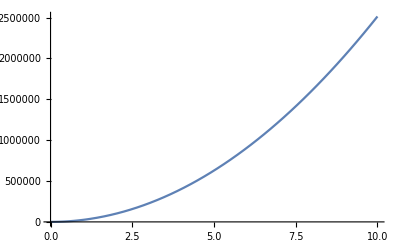

```mathematica
testT = 1000;
c=1;
kb=1;
Plot[u[x,testT], {x,0,10}]
Clear[c, kb];
```

```mathematica
Integrate[u[x,testT],{x,0,Infinity}]
```

Integrate::idiv: Integral of (8000 kb π x^2)/c^3 does not converge on {0,∞}.

∫_0^∞ (8000 kb π x^2)/c^3 ⅆx

Which violets energy conservation and contradicts experimental results... Classical physics breaks down.

### Quantum Derivation

In his attempts to derive the law for the spectral distribution of energy density of a body which is able to absorb all the radiant energy falling upon it, Planck was led to assume that the walls of such a body consist of harmonic oscillators, which exchange energy with the electromagnetic field inside the body only via integer multiples of a fundamental quantity . 

At this stage, to be consistent with another law that had been derived in a thermodynamical way and has and was hence of universal validity, the quantity  turned out to be proportional to the frequency of the radiation field, , and a new constant of nature, , with dimension [energy] [time] and since then called the Planck constant, was introduced for the first time. These problems are part of the general theory of heat radiation (Planck 1991).

#### Same Mode Counting

We use the same density of modes

```mathematica
dN/(V dν)
```

(8 π ν^2)/c^3

#### Quantum Energy Distribution

Now, instead of equipartition, each mode is a quantum harmonic oscillator with discrete energy levels:

```mathematica
e[n_, ν_]:=h n ν
```

The average energy per mode is given by the Boltzmann weighted average:

```mathematica
Clear[averageEnergy];
averageEnergy[ν_,T_]:=(h ν)/(ⅇ^(h ν/kb T)-1)
```

```mathematica
averageEnergy[ν,T]
```

(h ν)/(-1+ⅇ^((h T ν)/kb))

Note: This is the Bose-Einstein occupation number times the quantum energy. So, the energy density becomes:

```mathematica
quantumU[ν_, T_]:=(8 π ν^2)/c^3 averageEnergy[ν, T]
```

#### Planck’s Law

The final result  is known as the Planck distribution, and it matches experimental results perfectly.

```mathematica
quantumU[ν,T]
```

(8 h π ν^3)/(c^3 (-1+ⅇ^((h T ν)/kb)))

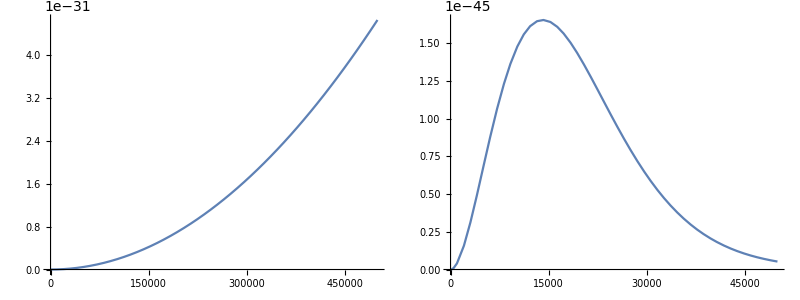

```mathematica
kb=10^-23;
c=3 10^8;
h=10^-32;
testT=200000;
Grid[{{Plot[u[x,testT],{x,0.1,500000} ],
Plot[quantumU[x,testT],{x,0.1,50000}]}}]
Clear[kb,c,testT,h]
```

## Einstein’s Explanation of the Photoelectric Effect

The photoelectric effect was a pivotal phenomenon that helped establish quantum theory. While Heinrich Hertz first observed the effect in 1887, it was Albert Einstein who provided the revolutionary explanation in 1905 that would earn him the Nobel Prize in Physics in 1921.

### The Classical Paradox

Before Einstein, physicists attempted to explain the photoelectric effect using classical electromagnetic theory. According to classical physics, light is a wave that carries energy continuously. When light shines on a metal surface, this energy should gradually accumulate in the electrons until they gain enough energy to escape the metal, regardless of the light’s frequency. Classical theory predicted:

Increasing light intensity should increase the energy of emitted electrons

All frequencies of light should be able to eject electrons, given sufficient intensity

There should be a delay between illumination and electron emission at low intensities

However, experiments revealed bewildering results:

The energy of emitted electrons depends only on the frequency of light, not its intensity

Below a certain threshold frequency, no electrons are emitted regardless of intensity

Electron emission occurs with no measurable delay, even at very low intensities

Let’s visualize the experimental setup and results using Mathematica:

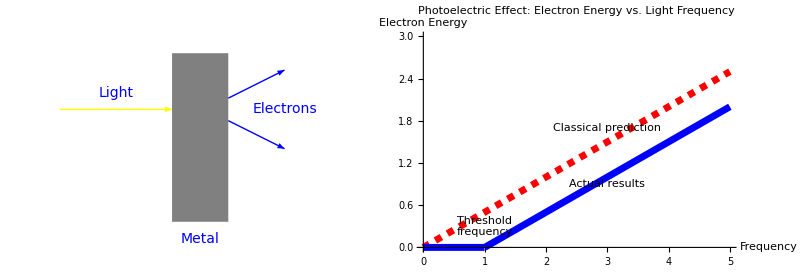

```mathematica
(* Create a simple diagram of the photoelectric effect experiment *)
photoelectricSetup = Graphics[{
   (* Metal plate *)
   Gray, Rectangle[{0, 0}, {1, 3}],
   (* Light beam *)
   Yellow, Arrow[{{-2, 2}, {0, 2}}],
   (* Ejected electrons *)
   Blue, Arrow[{{1, 2.2}, {2, 2.7}}],
   Blue, Arrow[{{1, 1.8}, {2, 1.3}}],
   (* Labels *)
   Text[Style["Light", 14], {-1, 2.3}],
   Text[Style["Metal", 14], {0.5, -0.3}],
   Text[Style["Electrons", 14], {2, 2}]
   }, PlotRange -> {{-2.5, 2.5}, {-0.5, 3.5}}, ImageSize -> 400];

(* Show the experimental results - Energy vs Frequency *)
classicalPrediction = Plot[0.5*f, {f, 0, 5}, 
   PlotStyle -> {Red, Dashed, Thickness[0.01]}, 
   PlotRange -> {{0, 5}, {0, 3}}];
   
quantumResult = Plot[If[f > 1, 0.5*(f - 1), 0], {f, 0, 5}, 
   PlotStyle -> {Blue, Thickness[0.01]}, 
   PlotRange -> {{0, 5}, {0, 3}}];
   
photoelectricPlot = Show[classicalPrediction, quantumResult, 
   PlotLabel -> "Photoelectric Effect: Electron Energy vs. Light Frequency", 
   AxesLabel -> {"Frequency", "Electron Energy"}, 
   Epilog -> {Text["Classical prediction", {3, 1.7}], 
       Text["Actual results", {3, 0.9}], 
       Text["Threshold\nfrequency", {1, 0.3}]},
   ImageSize -> 500];

GraphicsRow[{photoelectricSetup, photoelectricPlot}, Spacings -> 30]
```

### Einstein’s Quantum Solution

Einstein proposed a radical explanation: light consists of discrete packets of energy called photons (though he called them “light quanta” at the time). Each photon carries an energy proportional to its frequency:

where:

is the energy of a single photon

is Planck's constant (approximately  J·s)

is the frequency of the light

Einstein’s model explained the observations perfectly:

A single photon can eject at most one electron

Intensity affects the number of photons, not their individual energy

Electrons are ejected only if photon energy exceeds the metal’s work function

The maximum kinetic energy of ejected electrons follows a simple equation:
.
Where  is the work function of the metal (minimum energy needed to remove an electron). Let’s simulate the photoelectric effect with Mathematica:

```mathematica
(* Define constants *)
h = 6.626*10^-34; (* Planck's constant in J·s *)
eV = 1.602*10^-19; (* conversion from eV to Joules *)

(* Function to calculate maximum kinetic energy *)
maxKineticEnergy[frequency_, workFunction_] := Max[0, h*frequency - workFunction];

(* Interactive demonstration of the photoelectric effect *)
Manipulate[
  Module[{maxEnergy, photonEnergy},
    photonEnergy = h*frequency;
    maxEnergy = maxKineticEnergy[frequency, workFunction];
    
    Column[{
      (* Visualization *)
      Graphics[{
        (* Metal surface *)
        Gray, Rectangle[{-5, -2}, {0, 2}],
        
        (* Incoming photons *)
        Dynamic@Table[
          {Yellow, Disk[{-7 + Mod[t + i/3, 7], 0}, 0.2]},
          {i, 1, intensity}
        ],
        
        (* Electrons ejected (only if above threshold) *)
        If[photonEnergy > workFunction,
          Dynamic@Table[
            {Blue, Disk[{0.5 + Mod[t + i/5, 4], 0}, 0.15]},
            {i, 1, Min[intensity, 5]}
          ],
          {}
        ],
        
        (* Labels *)
        Text[Style["Metal", 14], {-2.5, 0}],
        Text[Style["Photons", 14], {-7, 1}],
        If[photonEnergy > workFunction,
          Text[Style["Electrons", 14], {2, 1}],
          {}
        ],
        
        (* Energy indicators *)
        Text[Style["Photon Energy: " <> ToString[Round[photonEnergy/eV, 0.01]] <> " eV", 12], {-6, -1.5}],
        Text[Style["Work Function: " <> ToString[Round[workFunction/eV, 0.01]] <> " eV", 12], {-2.5, -1.5}],
        If[photonEnergy > workFunction,
          Text[Style["Electron Energy: " <> ToString[Round[maxEnergy/eV, 0.01]] <> " eV", 12], {2, -1.5}],
          Text[Style["No electrons ejected", Red, 12], {2, -1.5}]
        ]
      }, PlotRange -> {{-8, 5}, {-2, 2}}, ImageSize -> 500],
      
      (* Energy diagram *)
      Plot[{workFunction, If[x >= frequency, workFunction, Infinity]}, {x, 0, 2*frequency},
        Filling -> {1 -> Bottom},
        FillingStyle -> LightGray,
        PlotStyle -> {{Gray, Thickness[0.01]}, {Red, Thickness[0.01]}},
        PlotRange -> {{0, 2*frequency}, {0, 1.5*photonEnergy}},
        AxesLabel -> {"Frequency", "Energy"},
        Epilog -> {
          Line[{{frequency, 0}, {frequency, photonEnergy}}],
          Text["Threshold", {frequency, photonEnergy/4}],
          If[photonEnergy > workFunction,
            {Blue, Arrow[{{frequency + frequency/10, workFunction}, {frequency + frequency/5, workFunction + maxEnergy}}],
             Text["Electron\nKinetic Energy", {frequency + frequency/4, workFunction + maxEnergy/2}]},
            {}
          ]
        }
      ]
    }]
  ],
  {{frequency, 5*10^14, "Light Frequency (Hz)"}, 1*10^14, 10*10^14, 0.1*10^14},
  {{workFunction, 3.5*10^-19, "Work Function (J)"}, 1*10^-19, 5*10^-19, 0.1*10^-19},
  {{intensity, 3, "Light Intensity"}, 1, 10, 1},
  {{t, 0, ""}, 0, 10, 0.1, AnimationRate -> 1, AnimationRunning -> True, ControlType -> None}
]
```

Let’s calculate the wavelength threshold for various metals:

Metal | Work Function (eV) | Threshold Wavelength (nm) | Visible Light?
Sodium | 2.28 | 544.2 | Yes
Aluminum | 4.08 | 304.1 | No
Copper | 4.7 | 264. | No
Silver | 4.26 | 291.3 | No
Gold | 5.1 | 243.3 | No
Platinum | 6.35 | 195.4 | No

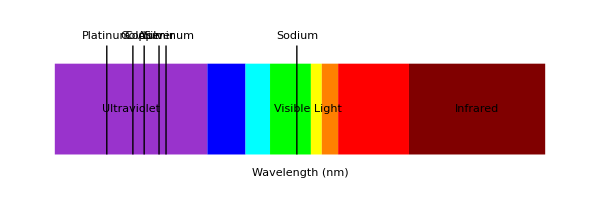

```mathematica
(* Work functions for common metals in electron volts *)
workFunctions = {
  {"Sodium", 2.28},
  {"Aluminum", 4.08},
  {"Copper", 4.70},
  {"Silver", 4.26},
  {"Gold", 5.10},
  {"Platinum", 6.35}
};

(* Calculate threshold wavelength *)
thresholdWavelength[workFunctionEV_] := (h*3*10^8)/(workFunctionEV*eV);

(* Create a table of results *)
Grid[
  Join[
    {{"Metal", "Work Function (eV)", "Threshold Wavelength (nm)", "Visible Light?"}},
    Table[
      With[{metal = wf[[1]], workFunction = wf[[2]], 
            wavelength = thresholdWavelength[wf[[2]]]*10^9},
        {metal, workFunction, Round[wavelength, 0.1], 
         If[380 <= wavelength <= 750, "Yes", "No"]}
      ],
      {wf, workFunctions}
    ]
  ],
  Frame -> All,
  Background -> {None, {LightYellow}}
]

(* Visualize the threshold wavelengths on the electromagnetic spectrum *)
spectrumColors = {
  {100, 380, RGBColor[0.6, 0.2, 0.8]}, (* ultraviolet *)
  {380, 450, Blue},                    (* violet *)
  {450, 495, Cyan},                    (* blue *)
  {495, 570, Green},                   (* green *)
  {570, 590, Yellow},                  (* yellow *)
  {590, 620, Orange},                  (* orange *)
  {620, 750, Red},                     (* red *)
  {750, 1000, RGBColor[0.5, 0, 0]}     (* infrared *)
};


spectrumBands=Table[{color[[3]],Rectangle[{color[[1]],0},{color[[2]],1}]},{color,spectrumColors}];

Graphics[{
  (* Draw spectrum bands *)
spectrumBands,
  
  (* Draw threshold markers *)
  Table[{Black, Line[{{thresholdWavelength[wf[[2]]]*10^9, 0}, 
          {thresholdWavelength[wf[[2]]]*10^9, 1.2}}],
         Text[wf[[1]], {thresholdWavelength[wf[[2]]]*10^9, 1.3}]},
    {wf, workFunctions}],
  
  (* Labels *)
  Text["Ultraviolet", {240, 0.5}],
  Text["Visible Light", {565, 0.5}],
  Text["Infrared", {875, 0.5}],
  Text["Wavelength (nm)", {550, -0.2}]
},
  PlotRange -> {{100, 1000}, {-0.3, 1.5}},
  ImageSize -> 600,
  AspectRatio -> 1/3
]
```

## The Bohr Model of the Atom

Niels Bohr’s atomic model, proposed in 1913, marked a critical transition between classical physics and the emerging quantum theory. While now superseded by more sophisticated quantum mechanical models, the Bohr model remains valuable as a conceptual stepping stone that successfully explained the hydrogen spectrum and introduced key quantum concepts.

### Historical Context

By the early 20th century, several key discoveries had undermined the classical understanding of atoms:

J.J. Thomson’s discovery of the electron (1897)

Ernest Rutherford’s gold foil experiment (1911), revealing a compact, positive nucleus

The precise, discrete spectral lines emitted by excited atoms

Rutherford proposed a “planetary model” with electrons orbiting the nucleus like planets around the sun. However, this model faced a devastating theoretical problem: according to classical electromagnetic theory, orbiting electrons should continuously emit radiation, spiral into the nucleus, and collapse the atom in microseconds.

### Bohr’s Revolutionary Postulates

Niels Bohr resolved this paradox by introducing radical assumptions that broke with classical physics :

Quantized orbits: Electrons can only occupy specific discrete orbits where the angular momentum is quantized (equal to an integer multiple of ħ = h/2π)

Stationary states: Electrons in these allowed orbits do not radiate energy despite their acceleration

Quantum jumps: Electrons change energy only by "jumping" between allowed energy levels, absorbing or emitting photons with energy equal to the difference between levels

Let’s implement the Bohr model in Mathematica:

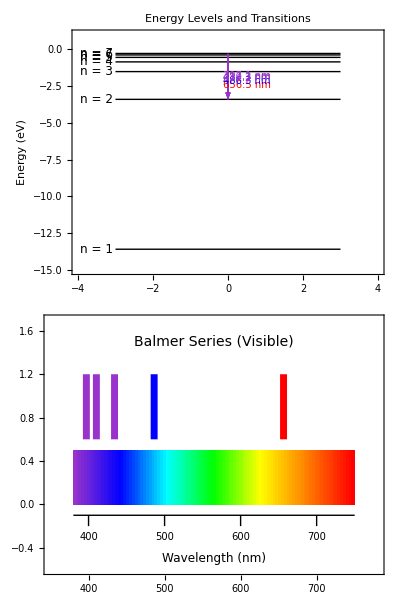

```mathematica
(*Constants*)
m=9.11*10^-31;             (*electron mass in kg*)
e=1.602*10^-19;            (*elementary charge in C*)
ϵ0=8.85*10^-12;   (*vacuum permittivity in F/m*)
h=6.626*10^-34;            (*Planck's constant in J·s*)
c=3*10^8;                  (*speed of light in m/s*)

(*Energy levels according to Bohr model for hydrogen*)
energyLevel[n_]:=-13.6/n^2;  (*in eV*)

(*Bohr radius for hydrogen-like atoms*)
bohrRadius[n_,Z_]:=0.0529*n^2/Z;  (*in nm*)

(*Create visualization of Bohr's model*)
bohrModelViz=Manipulate[
Module[
{radius,nucleusSize=0.01,electronSize=0.05},
radius=bohrRadius[n,1];
Graphics[
{
(*Nucleus*)
{Red,Disk[{0,0},nucleusSize]},
(*Electron orbits*)
Evaluate[
Table[
{LightGray,Circle[{0,0},bohrRadius[i,1]]},{i,1,5}
]
],
(*Current orbit highlight*)
{Blue,Thick,Circle[{0,0},radius]},
(*Electron*)
{Blue,Disk[radius*{Cos[angle],Sin[angle]},electronSize]},
(*Labels*)
Text[Style["n = "<>ToString[n],14],{0,-1.5*radius}],
Text[Style["Energy = "<>ToString[Round[energyLevel[n],0.01]]<>" eV",14],{0,-1.8*radius}],
Text[Style["Nucleus (proton)",12],{0,0.3}],
Text[Style["Electron",12],1.2*radius*{Cos[angle],Sin[angle]}]},
PlotRange->{{-3,3},{-3,3}},
ImageSize->400,
Frame->True,
FrameLabel->{"Position (nm)","Position (nm)"},
PlotLabel->Style["Bohr Model of Hydrogen Atom",16]
]
],
{{n,1,"Principal Quantum Number"},1,5,1},
{{angle,0,""},0,2 Pi,0.01,ControlType->None,AnimationRate->0.5,AnimationRunning->True}];

(*Create visualization of emission spectrum*)
transitionEnergy[nf_,ni_]:=energyLevel[nf]-energyLevel[ni];
wavelength[nf_,ni_]:=1240/Abs[transitionEnergy[nf,ni]];  (*in nm*)

spectrumViz=Module[
{transitions,spectrumColors,balmerTransitions},
(*Calculate transitions to n=2 (Balmer series)*)
balmerTransitions=Table[{i,2,wavelength[i,2]},{i,3,7}];
(*Assign colors based on wavelength*)spectrumColors=Table[
With[{λ=transition[[3]]},
{transition[[1]],
(*initial state*)
transition[[2]],
(*final state*)λ,
(*wavelength*)
Which[
(*color assignment*)
380<=λ<=450,RGBColor[0.6,0.2,0.8],(*violet*)
450<λ<=495,Blue,(*blue*)
495<λ<=570,Green,(*green*)
570<λ<=590,Yellow,(*yellow*)
590<λ<=620,Orange,(*orange*)
620<λ<=750,Red,(*red*)
True,
Gray (*outside visible*)]}],
{transition,balmerTransitions}
];
Column[{(*Energy level diagram*)Graphics[{(*Energy levels*)Table[{Line[{{-3,energyLevel[i]},{3,energyLevel[i]}}],Text[Style["n = "<>ToString[i],12],{-3.5,energyLevel[i]}]},{i,1,7}],(*Transitions*)Map[With[{n1=#[[1]],n2=#[[2]],λ=#[[3]],color=#[[4]]},{color,Arrow[{{0,energyLevel[n1]},{0,energyLevel[n2]}}],Text[Style[ToString[Round[λ,0.1]]<>" nm",10],{0.5,(energyLevel[n1]+energyLevel[n2])/2}]}]&,spectrumColors]},PlotRange->{{-4,4},{-15,1}},Frame->True,FrameLabel->{None,"Energy (eV)"},ImageSize->400,PlotLabel->Style["Energy Levels and Transitions",14]],
(*Spectral lines*)
Graphics[{
(*Background gradient representing visible spectrum*)
Table[
{
Blend[
{RGBColor[0.6,0.2,0.8],Blue,Cyan,Green,Yellow,Orange,Red},i/99],
Rectangle[{380+i*(750-380)/100,0},{380+(i+1)*(750-380)/100,0.5}]},{i,0,99}],
(*Scale*)
Line[{{380,-0.1},{750,-0.1}}],
Table[{Line[{{λ,-0.1},{λ,-0.2}}],
Text[Style[ToString[λ],10],{λ,-0.3}]},{λ,400,700,100}],
(*Spectral lines*)
Map[With[{λ=#[[3]],color=#[[4]]},
If[380<=λ<=750,{color,Thickness[0.01],Line[{{λ,0.6},{λ,1.2}}]}]]&,spectrumColors],
(*Labels*)
Text[Style["Balmer Series (Visible)",14],{565,1.5}],
Text[Style["Wavelength (nm)",12],{565,-0.5}]},
PlotRange->{{350,780},{-0.6,1.7}},ImageSize->500,
AspectRatio->1/3,Frame->True
]}]];

(*Display visualizations*)
Column[{bohrModelViz,spectrumViz},Spacings->2]
```

### Mathematical Formulation

Bohr' s theory can be derived from a few fundamental principles . For hydrogen - like atoms with atomic number  :

1. The electrostatic force provides the centripetal force necessary for circular motion :
   
2. The angular momentum is quantized :
   
From these conditions, we can derive the allowed radii :

Where  nm is the Bohr radius .
The allowed energy levels are :

Let' s calculate these values and compare with experimental data :

```mathematica
(* Create a table of energy levels *)
levels = Table[{n, energyLevel[n]}, {n, 1, 10}];

(* Calculate transition energies and wavelengths *)
transitionTable = Flatten[Table[
  With[{λ = wavelength[ni, nf], series = Which[
    nf == 1, "Lyman",
    nf == 2, "Balmer",
    nf == 3, "Paschen",
    nf == 4, "Brackett",
    nf == 5, "Pfund",
    True, "Other"
  ]},
  {ni, nf, series, energyLevel[ni], energyLevel[nf], 
   transitionEnergy[ni, nf], λ, 
   If[380 <= λ <= 750, "Visible", "Not visible"]}
  ],
  {nf, 1, 5}, {ni, nf + 1, nf + 5}
], 1];

(* Display the transition table *)
Grid[
  Join[
    {{"Initial n", "Final n", "Series", "Initial E (eV)", "Final E (eV)", 
      "Transition E (eV)", "Wavelength (nm)", "Visibility"}},
    transitionTable
  ],
  Frame -> All,
  Background -> {None, {LightYellow}},
  Dividers -> {{2 -> Black}, {2 -> Black}}
]

(* Compare with experimental values *)
experimentalData = {
  (* Series, n, Theoretical λ (nm), Experimental λ (nm) *)
  {"Balmer", 3, wavelength[3, 2], 656.3},
  {"Balmer", 4, wavelength[4, 2], 486.1},
  {"Balmer", 5, wavelength[5, 2], 434.1},
  {"Balmer", 6, wavelength[6, 2], 410.2},
  {"Lyman", 2, wavelength[2, 1], 121.6},
  {"Lyman", 3, wavelength[3, 1], 102.6},
  {"Paschen", 4, wavelength[4, 3], 1875.0},
  {"Paschen", 5, wavelength[5, 3], 1282.0}
};

(* Calculate accuracy *)
accuracy = Map[{#[[1]], #[[2]], #[[3]], #[[4]], 
  Round[100 * (1 - Abs[#[[3]] - #[[4]]]/{{#[[4]]}}), 0.01]} &, 
  experimentalData];

(* Display comparison *)
Grid[
  Join[
    {{"Series", "Transition", "Bohr Model (nm)", "Experimental (nm)", "Accuracy (%)"}},
    accuracy
  ],
  Frame -> All
]
```

Initial n | Final n | Series | Initial E (eV) | Final E (eV) | Transition E (eV) | Wavelength (nm) | Visibility
2 | 1 | Lyman | -3.4 | -13.6 | 10.2 | 121.569 | Not visible
3 | 1 | Lyman | -1.51111 | -13.6 | 12.0889 | 102.574 | Not visible
4 | 1 | Lyman | -0.85 | -13.6 | 12.75 | 97.2549 | Not visible
5 | 1 | Lyman | -0.544 | -13.6 | 13.056 | 94.9755 | Not visible
6 | 1 | Lyman | -0.377778 | -13.6 | 13.2222 | 93.7815 | Not visible
3 | 2 | Balmer | -1.51111 | -3.4 | 1.88889 | 656.471 | Visible
4 | 2 | Balmer | -0.85 | -3.4 | 2.55 | 486.275 | Visible
5 | 2 | Balmer | -0.544 | -3.4 | 2.856 | 434.174 | Visible
6 | 2 | Balmer | -0.377778 | -3.4 | 3.02222 | 410.294 | Visible
7 | 2 | Balmer | -0.277551 | -3.4 | 3.12245 | 397.124 | Visible
4 | 3 | Paschen | -0.85 | -1.51111 | 0.661111 | 1875.63 | Not visible
5 | 3 | Paschen | -0.544 | -1.51111 | 0.967111 | 1282.17 | Not visible
6 | 3 | Paschen | -0.377778 | -1.51111 | 1.13333 | 1094.12 | Not visible
7 | 3 | Paschen | -0.277551 | -1.51111 | 1.23356 | 1005.22 | Not visible
8 | 3 | Paschen | -0.2125 | -1.51111 | 1.29861 | 954.866 | Not visible
5 | 4 | Brackett | -0.544 | -0.85 | 0.306 | 4052.29 | Not visible
6 | 4 | Brackett | -0.377778 | -0.85 | 0.472222 | 2625.88 | Not visible
7 | 4 | Brackett | -0.277551 | -0.85 | 0.572449 | 2166.13 | Not visible
8 | 4 | Brackett | -0.2125 | -0.85 | 0.6375 | 1945.1 | Not visible
9 | 4 | Brackett | -0.167901 | -0.85 | 0.682099 | 1817.92 | Not visible
6 | 5 | Pfund | -0.377778 | -0.544 | 0.166222 | 7459.89 | Not visible
7 | 5 | Pfund | -0.277551 | -0.544 | 0.266449 | 4653.8 | Not visible
8 | 5 | Pfund | -0.2125 | -0.544 | 0.3315 | 3740.57 | Not visible
9 | 5 | Pfund | -0.167901 | -0.544 | 0.376099 | 3297.01 | Not visible
10 | 5 | Pfund | -0.136 | -0.544 | 0.408 | 3039.22 | Not visible

Series | Transition | Bohr Model (nm) | Experimental (nm) | Accuracy (%)
Balmer | 3 | 656.471 | 656.3 | {{99.97}}
Balmer | 4 | 486.275 | 486.1 | {{99.96}}
Balmer | 5 | 434.174 | 434.1 | {{99.98}}
Balmer | 6 | 410.294 | 410.2 | {{99.98}}
Lyman | 2 | 121.569 | 121.6 | {{99.97}}
Lyman | 3 | 102.574 | 102.6 | {{99.97}}
Paschen | 4 | 1875.63 | 1875. | {{99.97}}
Paschen | 5 | 1282.17 | 1282. | {{99.99}}

### Successes and Limitations

The Bohr model was remarkably successful in:

1. Explaining the hydrogen emission spectrum with unprecedented accuracy
2. Predicting the Rydberg constant value from fundamental constants
3. Introducing quantization and discrete energy levels
4. Establishing a theoretical framework for atomic physics

However, the model had significant limitations:

1. Failed to explain spectra of atoms with more than one electron
2. Could not explain the fine structure of spectral lines
3. Used an ad hoc mixture of classical and quantum concepts
4. Did not explain why only certain orbits were allowed

Keep in mind that this is hardly correct but just for the matter of checking out differences we’ve used a more (fairly more) corrected version of the equations.

## Wave-Particle Duality:The Cornerstone of Quantum Theory

## De Broglie’s Matter Waves Hypothesis

In 1924, Louis de Broglie presented a revolutionary doctoral thesis that would forever change our understanding of quantum mechanics. His central hypothesis—that particles such as electrons possess wave properties—provided a conceptual breakthrough that unified the seemingly contradictory wave and particle aspects of light and matter.

### The Dual Nature of Light

By the early 1920s, physicists faced a profound puzzle: light exhibited both wave-like behaviors (interference, diffraction) and particle-like behaviors (photoelectric effect, Compton scattering). Einstein had shown that light waves could behave as particles (photons), but de Broglie made the daring intellectual leap in the opposite direction—proposing that particles traditionally thought of as corpuscular could exhibit wave-like properties.

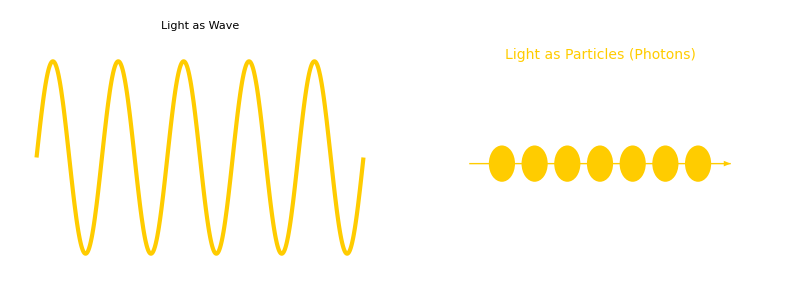
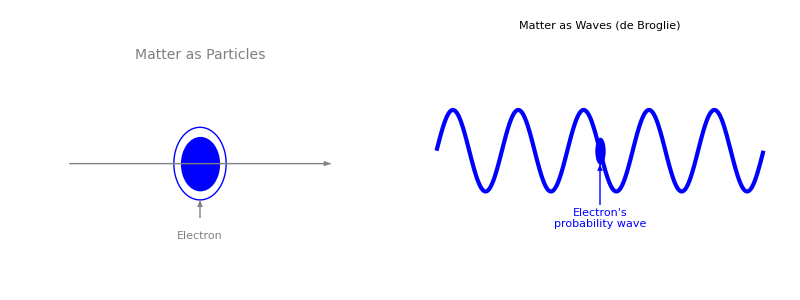
Wave-Particle Duality
-Graphics-

-Graphics-

```mathematica
(*Visualization of wave-particle duality*)
dualityViz=Column[{
(*Title*)
Text[Style["Wave-Particle Duality",Bold,16]],
(*Light behavior*)Grid[
{
{
(*Light as wave*)
Plot[Sin[5 x],{x,0,2 Pi},
PlotStyle->{Thickness[0.01],
RGBColor[1,0.8,0]},
PlotLabel->Style["Light as Wave",14],
Axes->False,
PlotRange->{{0,2 Pi},{-1.2,1.2}},
ImageSize->300],
(*Light as particles*)
Graphics[
{
(*Photon path*)
RGBColor[1,0.8,0],
Arrow[{{0,0},{4,0}}],
(*Photon particles*)
Table[{RGBColor[1,0.8,0],Disk[{x,0},0.2]},{x,0.5,3.5,0.5}],
(*Labels*)
Text[Style["Light as Particles (Photons)",14],{2,1.2}]},PlotRange->{{-0.5,4.5},{-1.2,1.5}},ImageSize->300]}}],
(*Spacer*)
Spacer[10],
(*De Broglie's hypothesis*)
Grid[{{
(*Matter as particles*)
Graphics[{
(*Electron*)
Blue,
Disk[{2,0},0.3],Circle[{2,0},0.4,{0,2Pi}],
(*Path*)
Gray,
Arrow[{{0,0},{4,0}}],
(*Labels*)
Text[Style["Matter as Particles",14],{2,1.2}],
Text["Electron",{2,-0.8}],Arrow[{{2,-0.6},{2,-0.4}}]},
PlotRange->{{-0.5,4.5},{-1.2,1.5}},ImageSize->300],
(*De Broglie's hypothesis:Matter as waves*)
Plot[0.3*Sin[5 x]+0.7,{x,0,2 Pi},
PlotStyle->{Thickness[0.01],Blue},
PlotLabel->Style["Matter as Waves\n(de Broglie)",14],
Axes->False,
PlotRange->{{0,2 Pi},{-0.2,1.5}},
Epilog->{Blue,Disk[{Pi,0.7},0.1],
Text["Electron's\nprobability wave",{Pi,0.2}],
Arrow[{{Pi,0.3},{Pi,0.6}}]},
ImageSize->300]}
}]}
]
```

### The de Broglie Wavelength

The central equation of de Broglie’s hypothesis relates the wavelength of a matter wave to the momentum of the particle:


Where:

is the de Broglie wavelength

is Planck’s constant ( J·s)

is the momentum of the particle

is the mass of the particle

v is the velocity of the particle

This elegant equation suggests that all matter has an associated wavelength that is inversely proportional to its momentum. Let’s explore this relationship with Mathematica:

```mathematica
(* Constants *)
h=6.626 10^-34;
massOfElectron=9.11 10^-31;
massOfProton= 1.673 10^-27;
massOfNeutron=1.675 10^-27;
eV=1.602 10^-19;

(*De Broglie wavelength function*)
deBroglieWavelength[mass_,velocity_]:=h/(mass*velocity);
deBroglieWavelengthEnergy[mass_,energy_]:=h/Sqrt[2*mass*energy];
```

```mathematica
(*Interactive demonstration of de Broglie wavelength*)
Manipulate[Module[{λ,p,v,particleMass},(*Set the particle mass based on selection*)particleMass=Which[particle=="Electron",massOfElectron,particle=="Proton",massOfProton,particle=="Neutron",massOfNeutron,particle=="Sodium atom",3.82*10^-26];
(*Calculate wavelength based on energy*)λ=deBroglieWavelengthEnergy[particleMass,energy*eV];
v=Sqrt[2*energy*eV/particleMass];
p=particleMass*v;
Column[{(*Display calculated values*)Grid[{{"Particle:",particle},{"Mass:",ToString[ScientificForm[particleMass]]<>" kg"},{"Energy:",ToString[energy]<>" eV"},{"Velocity:",ToString[ScientificForm[v/1000]]<>" km/s ("<>ToString[NumberForm[100*v/299792458,{3,2}]]<>"% of c)"},{"de Broglie wavelength:",ToString[NumberForm[λ*10^9,{4,8}]]<>" nm"}}],(*Visualization*)Graphics[{(*Particle representation*)Which[particle=="Electron",{Blue,Disk[{0,0},0.05]},particle=="Proton",{Red,Disk[{0,0},0.08]},particle=="Neutron",{Gray,Disk[{0,0},0.08]},particle=="Sodium atom",{Yellow,Disk[{0,0},0.12]}],(*Associated wave-scaled for visualization*)Blue,Thickness[0.005],Line[Table[{x,0.2*Sin[2*Pi*x/0.3]},{x,-2,2,0.01}]],(*Wavelength indicator*)Red,Arrow[{{-0.3,-0.15},{0,-0.15}}],Arrow[{{0,-0.15},{0.3,-0.15}}],Text["λ",{0,-0.25}],(*Context objects for scale reference*)Gray,Line[{{-2,-0.5},{2,-0.5}}],(*"surface"*)(*Scale references*)Which[λ>10^-9,{Text["Scale reference: Human hair (~100 μm)",{0,-0.7}]},λ>10^-10,{Text["Scale reference: Atom (~0.1 nm)",{0,-0.7}]},True,{Text["Scale reference: Nucleus (~1 fm)",{0,-0.7}]}]},PlotRange->{{-2,2},{-1,1}},ImageSize->400],(*Comparison with everyday objects*)Text[Style["Comparative Wavelengths:",Bold,12]],Grid[{{"Object","Typical de Broglie wavelength"},{"Electron in CRT","0.01 - 0.1 nm"},{"Thermal neutron","0.1 - 0.2 nm"},{"Baseball (40 m/s)","10^-34 m (undetectable)"},{"Human walking","10^-36 m (undetectable)"}},Frame->All]}]],{{particle,"Electron","Particle type"},{"Electron","Proton","Neutron","Sodium atom"}},{{energy,100,"Energy (eV)"},1,10000,1,Appearance->"Labeled"}]
```

### Experimental Confirmation

De Broglie' s hypothesis initially seemed like a mathematical curiosity with little experimental backing . However, in 1927, Clinton Davisson and Lester Germer at Bell Labs accidentally discovered electron diffraction while studying electron scattering from nickel crystals . Their experiment showed that electrons could indeed produce diffraction patterns—a phenomenon previously associated only with waves .
   
Let' s model the Davisson - Germer experiment :

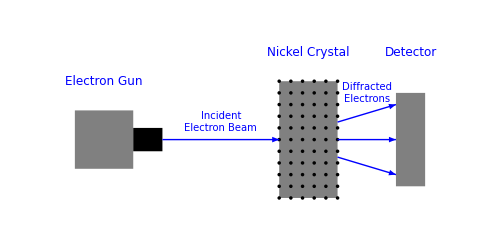

-Graphics-

-Graphics-

```mathematica
(* Davisson-Germer experiment visualization *)
davisson = Module[{},
  Graphics[{
    (* Electron gun *)
    Gray, Rectangle[{-4, -0.5}, {-3, 0.5}],
    Black, Rectangle[{-3, -0.2}, {-2.5, 0.2}],
    
    (* Nickel crystal *)
    Gray, Polygon[{{-0.5, -1}, {0.5, -1}, {0.5, 1}, {-0.5, 1}}],
    
    (* Crystal lattice points *)
    Table[{Black, Disk[{-0.5 + 0.2*i, -1 + 0.2*j}, 0.03]}, 
          {i, 0, 5}, {j, 0, 10}],
    
    (* Detector *)
    Gray, Rectangle[{1.5, -0.8}, {2, 0.8}],
    
    (* Diffracted electrons *)
    Blue, Arrow[{{-2.5, 0}, {-0.5, 0}}],
    
    (* Diffraction pattern *)
    Blue, Arrow[{{0.5, 0.3}, {1.5, 0.6}}],
    Blue, Arrow[{{0.5, 0}, {1.5, 0}}],
    Blue, Arrow[{{0.5, -0.3}, {1.5, -0.6}}],
    
    (* Labels *)
    Text[Style["Electron Gun", 12], {-3.5, 1}],
    Text[Style["Nickel Crystal", 12], {0, 1.5}],
    Text[Style["Detector", 12], {1.75, 1.5}],
    Text[Style["Incident\nElectron Beam", 10], {-1.5, 0.3}],
    Text[Style["Diffracted\nElectrons", 10], {1, 0.8}]
  },
  PlotRange -> {{-4.5, 2.5}, {-1.5, 2}},
  ImageSize -> 500]
]

(* Diffraction pattern simulation *)
diffractionPattern = DensityPlot[
  Sum[Cos[5*((x - 0.5*i)^2 + (y - 0.5*j)^2)]^2, {i, -2, 2}, {j, -2, 2}],
  {x, -3, 3}, {y, -3, 3},
  ColorFunction -> "Rainbow",
  PlotPoints -> 100,
  PlotLabel -> Style["Electron Diffraction Pattern", 14],
  Frame -> True,
  FrameLabel -> {"Position", "Position"},
  ImageSize -> 400
]

(* Display both visualizations *)
Column[{davisson, diffractionPattern}]
```

Another crucial confirmation came from G.P. Thomson (son of J.J. Thomson, who discovered the electron), who independently observed electron diffraction by passing electrons through thin metal foils. Ironically, J.J. Thomson had received the Nobel Prize for proving that electrons were particles, while his son later shared the Nobel Prize for proving electrons were also waves!

### Bohr Model Reinterpreted

De Broglie’s hypothesis provided a natural explanation for Bohr’s quantization conditions. He proposed that electrons in allowed Bohr orbits must form standing waves around the nucleus. For a wave to be stable (standing), its wavelength must fit the orbit circumference an integer number of times:

```mathematica
(*Standing wave visualization*)standingWaveViz=Manipulate[Module[{radius=1.0},Column[{Text[Style["De Broglie's Standing Wave Condition",Bold,14]],Graphics[{(*Nucleus*)Red,Disk[{0,0},0.1],(*Orbit*)Gray,Circle[{0,0},radius],(*Standing wave*)Blue,Thick,Line[Table[{radius*Cos[t],radius*Sin[t]+0.1*Sin[n*t]},{t,0,2*Pi,0.01}]],(*Labels*)Text[Style["n = "<>ToString[n],14],{0,-1.3}],Text[Style[ToString[n]<>" wavelengths fit around the orbit",12],{0,-1.5}],Text[Style["Nucleus",12],{0,0.3}],(*Wavelength indicator*)If[n>=1,{Red,Arrow[{{radius*Cos[0],radius*Sin[0]},{radius*Cos[2*Pi/n],radius*Sin[2*Pi/n]}}],Text["λ",{radius*Cos[Pi/n],radius*Sin[Pi/n]-0.2}]},{}]},PlotRange->{{-1.7,1.7},{-1.7,1.7}},ImageSize->400],Text[Style["Mathematical Relationship:",Bold,12]],Text["n * λ = 2π * r"],Text["For quantum number n = "<>ToString[n]<>", exactly "<>ToString[n]<>" wavelengths fit around the orbit circumference"]}]],{{n,3,"Quantum Number (n)"},1,10,1,Appearance->"Labeled"}];

(*Combination of Bohr model and de Broglie waves*)
deBroglieBohr=Column[{standingWaveViz,(*Explanation of how de Broglie resolved Bohr's ad hoc assumption*)Panel[Column[{Text[Style["How De Broglie's Hypothesis Explains Bohr's Quantization",Bold,14]],"",Text["Bohr's model required the arbitrary assumption that angular momentum is quantized:"],Text["mvr = nħ"],"",Text["De Broglie showed this follows naturally from the wave nature of electrons:"],Text["1. Electron wavelength: λ = h/mv"],Text["2. Standing wave condition: nλ = 2πr"],"",Text["Combining these equations:"],Text["n(h/mv) = 2πr"],Text["nh = 2πmvr"],Text["mvr = nh/2π = nħ"],"",Text[Style["This derives Bohr's quantization condition from more fundamental principles!",Bold,12]]}],ImageMargins->10]}]
```

How De Broglie's Hypothesis Explains Bohr's Quantization

Bohr's model required the arbitrary assumption that angular momentum is quantized:
mvr = nħ

De Broglie showed this follows naturally from the wave nature of electrons:
1. Electron wavelength: λ = h/mv
2. Standing wave condition: nλ = 2πr

Combining these equations:
n(h/mv) = 2πr
nh = 2πmvr
mvr = nh/2π = nħ

This derives Bohr's quantization condition from more fundamental principles!

### Beyond Atoms: Matter Waves in Modern Physics

De Broglie' s matter wave hypothesis extends far beyond the hydrogen atom . It applies to all matter, though the wavelengths for macroscopic objects are typically too small to detect . For subatomic particles, however, the wave nature becomes essential :

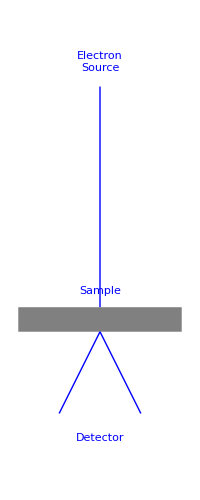
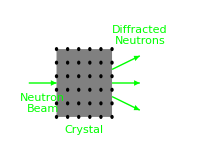
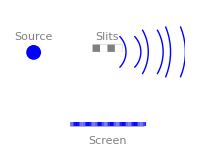
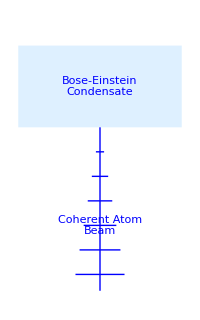
Object | de Broglie Wavelength | Object Size | Wave Effects?
Electron (1 eV) | 1.23 nm | 0.1 nm | Observable
Electron (100 keV) | 3.88 pm | 0.1 nm | Negligible
Neutron (thermal) |          26
1.47 × 10 nm | 0.1 nm | Observable
Helium atom (room temp) |          25
7.38 × 10 nm | 0.1 nm | Observable
Dust particle (1 μm) | 0.00 pm | 1 μm | Negligible
Baseball (40 m/s) |          -22
1.14 × 10 pm | 7.3 cm | Negligible
Applications of Matter Waves in Modern Physics
Electron Microscopy
-Graphics-
• Resolution limited by λ = h/mv
• 100 keV electrons: λ ≈ 4 pm
• Far better than optical microscopes | Neutron Diffraction
-Graphics-
• Thermal neutrons: λ ≈ 0.2 nm
• Penetrates materials deeply
• Sensitive to magnetic structure
Quantum Interference
-Graphics-
• Matter waves interfere with themselves
• Even single particles show interference
• Foundational to quantum mechanics | Modern Applications
• Electron Lithography
• Scanning Tunneling Microscopy
• Atom Interferometry
• Quantum Computing
• Neutron Scattering Analysis
• Atom Lasers
-Graphics-

```mathematica
(*Constants-make sure these are defined*)h=6.626*10^-34;    (*Planck's constant in J⋅s*)
massOfElectron=9.11*10^-31;    (*Mass of electron in kg*)
kB=1.38*10^-23;    (*Boltzmann constant*)
eV=1.602*10^-19;   (*Electron volt in Joules*)

(*De Broglie wavelength function if not already defined*)
deBroglieWavelength[mass_,velocity_]:=h/(mass*velocity);

(*Table of de Broglie wavelengths for various objects*)
wavelengthTable=Module[{objects,masses,velocities,wavelengths,wavelengthsText},objects={"Electron (1 eV)","Electron (100 keV)","Neutron (thermal)","Helium atom (room temp)","Dust particle (1 μm)","Baseball (40 m/s)"};
masses={massOfElectron,massOfElectron,1.675*10^-27,6.646*10^-27,10^-15,0.145};
velocities={Sqrt[2*eV/massOfElectron],(*1 eV electron*)Sqrt[2*100000*eV/massOfElectron],(*100 keV electron*)Sqrt[3*kB*293/1.675*10^-27],(*thermal neutron at room temp*)Sqrt[3*kB*293/6.646*10^-27],(*helium at room temp*)0.001,(*dust particle at 1 mm/s*)40                                        (*baseball at 40 m/s*)};
wavelengths=deBroglieWavelength[#1,#2]&@@@Transpose[{masses,velocities}];
(*Convert to appropriate units*)wavelengthsText=Map[If[#>10^-10,ToString[NumberForm[#*10^9,{4,2}]]<>" nm",ToString[NumberForm[#*10^12,{4,2}]]<>" pm"]&,wavelengths];
(*Compare to object size*)objectSizes={"0.1 nm","0.1 nm","0.1 nm","0.1 nm","1 μm","7.3 cm"};
(*Create comparison table*)Grid[Join[{{"Object","de Broglie Wavelength","Object Size","Wave Effects?"}},Transpose[{objects,wavelengthsText,objectSizes,Map[If[#>10^-11,"Observable","Negligible"]&,wavelengths]}]],Frame->All,Background->{None,{LightYellow}}]];

(*Applications of matter waves*)
matterWaveApplications=Column[{Text[Style["Applications of Matter Waves in Modern Physics",Bold,16]],Grid[{{(*Electron Microscopy*)Panel[Column[{Text[Style["Electron Microscopy",Bold,14]],Graphics[{(*Sample*)Gray,Rectangle[{0,0},{2,0.3}],(*Electron beam*)Blue,Line[{{1,3},{1,0.3}}],(*Scattered electrons*)Blue,Line[{{1,0},{0.5,-1}}],Blue,Line[{{1,0},{1.5,-1}}],(*Labels*)Text["Electron\nSource",{1,3.3}],Text["Sample",{1,0.5}],Text["Detector",{1,-1.3}]},PlotRange->{{0,2},{-1.5,3.5}},ImageSize->200],Text["• Resolution limited by λ = h/mv"],Text["• 100 keV electrons: λ ≈ 4 pm"],Text["• Far better than optical microscopes"]}]],(*Neutron Diffraction*)Panel[Column[{Text[Style["Neutron Diffraction",Bold,14]],Graphics[{(*Crystal*)Gray,Rectangle[{0.5,0.5},{1.5,1.5}],(*Atoms in crystal*)Table[{Black,Disk[{0.5+0.2*i,0.5+0.2*j},0.03]},{i,0,5},{j,0,5}],(*Neutron beam*)Green,Arrow[{{0,1},{0.5,1}}],(*Diffracted neutrons*)Green,Arrow[{{1.5,1.2},{2,1.4}}],Green,Arrow[{{1.5,1},{2,1}}],Green,Arrow[{{1.5,0.8},{2,0.6}}],(*Labels*)Text["Neutron\nBeam",{0.25,0.7}],Text["Crystal",{1,0.3}],Text["Diffracted\nNeutrons",{2,1.7}]},PlotRange->{{-0.2,2.2},{0,2}},ImageSize->200],Text["• Thermal neutrons: λ ≈ 0.2 nm"],Text["• Penetrates materials deeply"],Text["• Sensitive to magnetic structure"]}]]},{(*Quantum Interference*)Panel[Column[{Text[Style["Quantum Interference",Bold,14]],Graphics[{(*Double slit*)Gray,Rectangle[{0.8,0},{1.2,0.1}],White,Rectangle[{0.9,0},{1,0.1}],White,Rectangle[{1.1,0},{1.2,0.1}],(*Source*)Blue,Disk[{0,0},0.1],(*Waves*)Blue,Circle[{0.95,0},0.3,{-Pi/4,Pi/4}],Blue,Circle[{0.95,0},0.6,{-Pi/6,Pi/6}],Blue,Circle[{0.95,0},0.9,{-Pi/8,Pi/8}],Blue,Circle[{1.15,0},0.3,{-Pi/4,Pi/4}],Blue,Circle[{1.15,0},0.6,{-Pi/6,Pi/6}],Blue,Circle[{1.15,0},0.9,{-Pi/8,Pi/8}],(*Screen*)Gray,Line[{{0.5,-1},{1.5,-1}}],(*Interference pattern*)Table[{Blend[{White,Blue},0.5+0.5*Sin[20*x]^2],Rectangle[{0.5+x,-1},{0.5+x+0.02,-0.95}]},{x,0,1,0.02}],(*Labels*)Text["Source",{0,0.2}],Text["Slits",{1,0.2}],Text["Screen",{1,-1.2}]},PlotRange->{{-0.2,2},{-1.3,0.5}},ImageSize->200],Text["• Matter waves interfere with themselves"],Text["• Even single particles show interference"],Text["• Foundational to quantum mechanics"]}]],(*Practical Applications*)Panel[Column[{Text[Style["Modern Applications",Bold,14]],Text["• Electron Lithography"],Text["• Scanning Tunneling Microscopy"],Text["• Atom Interferometry"],Text["• Quantum Computing"],Text["• Neutron Scattering Analysis"],Text["• Atom Lasers"],Graphics[{(*Atom laser illustration*)LightBlue,Rectangle[{0,0},{2,1}],Blue,Line[{{1,0},{1,-2}}],Blue,Line[{{0.95,-0.3},{1.05,-0.3}}],Blue,Line[{{0.9,-0.6},{1.1,-0.6}}],Blue,Line[{{0.85,-0.9},{1.15,-0.9}}],Blue,Line[{{0.8,-1.2},{1.2,-1.2}}],Blue,Line[{{0.75,-1.5},{1.25,-1.5}}],Blue,Line[{{0.7,-1.8},{1.3,-1.8}}],Text["Bose-Einstein\nCondensate",{1,0.5}],Text["Coherent Atom\nBeam",{1,-1.2}]},PlotRange->{{0,2},{-2,1.2}},ImageSize->200]}]]}}]}];

(*Show all visualizations*)
Column[{wavelengthTable,matterWaveApplications}]
```

## The Double-Slit Experiment and Its Implications

### Historical Context

The double-slit experiment, first performed by Thomas Young in 1801, has evolved into one of the most profound demonstrations of quantum mechanical principles. Originally designed to investigate the wave nature of light, this deceptively simple experiment has become a cornerstone for understanding quantum behavior and the wave-particle duality that lies at the heart of quantum mechanics.

Let’s begin by exploring this experiment and its implications using Mathematica to visualize the concepts.

### Classical Wave Interference

First, let’s review classical wave interference patterns to establish a baseline understanding. When coherent waves pass through two narrow apertures (slits), they create a characteristic interference pattern on a screen placed behind the slits.

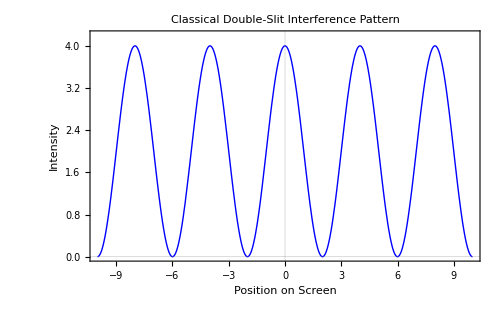

```mathematica
(* Parameters for visualization *)
wavelength = 1;
slitSeparation = 5;
distanceToScreen = 20;
screenWidth = 20;

(* Path difference function *)
pathDifference[x_] := slitSeparation*x/distanceToScreen;

(* Intensity function for classical waves *)
intensity[x_] := 4*Cos[Pi*slitSeparation*x/(wavelength*distanceToScreen)]^2;

(* Visualize classical interference pattern *)
classicalPlot = Plot[intensity[x], {x, -screenWidth/2, screenWidth/2},
  PlotRange -> {0, 4.2},
  PlotStyle -> {Thick, Blue},
  AxesLabel -> {"Position on Screen", "Intensity"},
  PlotLabel -> "Classical Double-Slit Interference Pattern",
  PlotTheme -> "Scientific",
  ImageSize -> 500]
```

The pattern shown above is characteristic of waves. The bright fringes (maxima) occur where the path difference between waves from the two slits equals an integer multiple of the wavelength, resulting in constructive interference. Dark fringes (minima) occur where the path difference equals a half-integer multiple of the wavelength, resulting in destructive interference.

### Quantum Double-Slit: Particles Behaving as Waves

Now, let’s consider what happens when we perform the double-slit experiment with quantum particles like electrons. According to classical mechanics, we would expect two bands directly behind each slit. However, experiments reveal a startling result: quantum particles create an interference pattern similar to waves, even when fired one at a time!

Let’s simulate this quantum behavior:

```mathematica
Manipulate[Module[{slitSeparation=1,wavelength=0.5,screenDistance=5,intensityClassical,intensityQuantum,x,xs,nParticles},
xs=Subdivide[-10,10,1000];
intensityClassical[x_]:=Cos[Pi*slitSeparation*x/(wavelength*screenDistance)]^2;
intensityQuantum[x_]:=If[
nParticles<100,
Module[{rng=RandomReal[{-10,10},nParticles]},Total[Table[Exp[-(x-xi)^2],{xi,rng}]]],
intensityClassical[x]];
ListLinePlot[
Table[{x,intensityQuantum[x]},{x,xs}],
PlotRange->All,AxesLabel->{"x (screen position)","Intensity"},
PlotLabel->"Quantum vs Classical Double Slit ("<>ToString[nParticles]<>" particles)",
PlotStyle->Blue]],
{{nParticles,10,"Number of Particles"},
1,
1000,
1}]
```

To visualize the buildup of individual particle detections over time, we can simulate the gradual emergence of the interference pattern:

```

## The Measurement Paradox

The most astonishing aspect of the double-slit experiment emerges when we attempt to determine which path each particle takes. Let’s use Mathematica to illustrate what happens when we place detectors at the slits:

```mathematica
(* Function for single-slit pattern *)
singleSlitPattern[x_, slitPosition_] := 
  Sinc[3 (x - slitPosition)]^2;

(* Plot showing the effect of measurement *)
measuredPlot = Plot[
  {singleSlitPattern[x, -slitSeparation/2] + singleSlitPattern[x, slitSeparation/2], 
   probability[x]/Max[Table[probability[y], {y, -screenWidth/2, screenWidth/2, 0.1}]]},
  {x, -screenWidth/2, screenWidth/2},
  PlotStyle -> {{Thick, Purple}, {Thick, Red, Dashed}},
  PlotLegends -> {“With Path Measurement”, “Without Measurement”},
  AxesLabel -> {“Position on Screen”, “Normalized Intensity”},
  PlotLabel -> “The Measurement Effect in Double-Slit Experiment”,
  PlotTheme -> “Scientific”,
  ImageSize -> 600]
```

When we observe which slit each particle passes through, the interference pattern disappears, and we instead see the classical sum of two single-slit patterns. This demonstrates a fundamental principle of quantum mechanics: the act of measurement affects the system being measured.

## Interpretational Implications

The double-slit experiment reveals several profound implications:

1. **Wave-Particle Duality**: Quantum entities exhibit both wave-like and particle-like properties, depending on how we observe them.

2. **Complementarity**: Certain pairs of properties cannot be simultaneously observed with precision. When we observe the path, we lose the interference pattern.

3. **Superposition**: Before detection, particles exist in a superposition of states, mathematically represented as:

```mathematica
(* Superposition state *)
psiSuperposition = 
  HoldForm[Psi[x] = a*Psi1[x] + b*Psi2[x]];
  
TraditionalForm[psiSuperposition]
```

4. **Collapse of the Wavefunction**: Measurement causes the superposition to “collapse” into a definite state:

```mathematica
(* Visual representation of wavefunction collapse *)
animateCollapse = Manipulate[
  Plot[
    Exp[-5 (1 - t) (x - 2)^2] + Exp[-5 (1 - t) (x + 2)^2] + t*6*Exp[-10 (x - 2)^2],
    {x, -5, 5}, 
    PlotRange -> {0, 6},
    PlotLabel -> If[t < 1, “Superposition State”, “Collapsed State”],
    AxesLabel -> {“Position”, “Ψ.b2”},
    PlotStyle -> Directive[Thick, ColorData[“Rainbow”][t]],
    ImageSize -> 500
  ],
  {t, 0, 1, 0.05}
]

frames = Table[
  Plot[
    Exp[-5 (1 - t) (x - 2)^2] + Exp[-5 (1 - t) (x + 2)^2] + t*6*Exp[-10 (x - 2)^2],
    {x, -5, 5}, 
    PlotRange -> {0, 6},
    PlotLabel -> If[t < 1, “Superposition State”, “Collapsed State”],
    AxesLabel -> {“Position”, “Ψ.b2”},
    PlotStyle -> Directive[Thick, ColorData[“Rainbow”][t]],
    ImageSize -> 350
  ],
  {t, {0, 0.3, 0.6, 1}}
];

Grid[{{frames[[1]], frames[[2]]}, {frames[[3]], frames[[4]]}}]
```

The double-slit experiment stands as one of the most elegant demonstrations that quantum mechanics represents a fundamental departure from classical physics. It forces us to reconsider our intuitive notions of reality and points to a quantum world that defies classical description.

## Interactive Exploration

Let’s create an interactive demonstration that allows us to explore how changing parameters affects the interference pattern:

```mathematica
Manipulate[
  Module[{k = 2 Pi/lambda, d = slitDistance/2},
    Plot[
      4*Cos[k*d*x/L]^2, 
      {x, -10, 10},
      PlotRange -> {0, 4.2},
      AxesLabel -> {“Position (x)”, “Intensity”},
      PlotLabel -> “Double-Slit Interference Pattern”,
      PlotStyle -> Directive[Thick, Hue[0.6]],
      ImageSize -> 500
    ]
  ],
  {{lambda, 1, “Wavelength”}, 0.5, 3, 0.1},
  {{slitDistance, 5, “Slit Separation”}, 1, 10, 0.5},
  {{L, 20, “Screen Distance”}, 10, 50, 5},
  ControlPlacement -> Bottom
]
```

# Heisenberg’s Uncertainty Principle

## Historical Development

Werner Heisenberg formulated his famous uncertainty principle in 1927, establishing one of the fundamental limitations inherent in quantum mechanics. Unlike classical physics, where all properties of a system can in principle be measured with arbitrary precision, quantum mechanics reveals intrinsic limits to what can be simultaneously known about complementary variables.

## Mathematical Formulation

The uncertainty principle is most commonly expressed as a relationship between position (x) and momentum (p):

```mathematica
uncertaintyRelation = 
  HoldForm[Δx*Δp >= ℏ/2];

TraditionalForm[uncertaintyRelation]
```

Where:
- Δx represents the standard deviation in position measurements
- Δp represents the standard deviation in momentum measurements
- ℏ is the reduced Planck constant (h/2π)

This inequality means that the more precisely we know a particle’s position, the less precisely we can know its momentum, and vice versa.

The principle applies to other complementary pairs of observables as well. For energy and time:

```mathematica
energyTimeUncertainty = 
  HoldForm[ΔE*Δt >= ℏ/2];

TraditionalForm[energyTimeUncertainty]
```

## Quantum Mechanical Basis

The uncertainty principle arises naturally from the wave nature of quantum entities. Let’s use Mathematica to visualize this concept through wavefunctions:

```mathematica
(* Define a Gaussian wavepacket *)
gaussianWavepacket[x_, σ_] := (2*Pi*σ^2)^(-1/4)*Exp[-x^2/(4*σ^2)];

(* Calculate momentum-space wavefunction (Fourier transform) *)
momentumWavefunction[p_, σ_] := (2*σ/Sqrt[Pi])^(1/2)*Exp[-p^2*σ^2];

(* Plot position-space wavefunctions with different widths *)
positionPlot = Plot[
  Evaluate[Table[
    Abs[gaussianWavepacket[x, σ]]^2, 
    {σ, {0.5, 1, 2}}
  ]],
  {x, -5, 5},
  PlotRange -> {0, 1.2},
  PlotStyle -> {Red, Green, Blue},
  PlotLegends -> 
    Placed[LineLegend[{Red, Green, Blue}, 
      {“σ = 0.5 (Localized)”, “σ = 1”, “σ = 2 (Spread out)”}], {0.5, 0.8}],
  AxesLabel -> {“Position (x)”, “Probability Density |Ψ(x)|.b2”},
  PlotLabel -> “Position-Space Wavefunctions”,
  ImageSize -> 500
]

(* Plot corresponding momentum-space wavefunctions *)
momentumPlot = Plot[
  Evaluate[Table[
    Abs[momentumWavefunction[p, σ]]^2, 
    {σ, {0.5, 1, 2}}
  ]],
  {p, -5, 5},
  PlotRange -> {0, 1.2},
  PlotStyle -> {Red, Green, Blue},
  PlotLegends -> 
    Placed[LineLegend[{Red, Green, Blue}, 
      {“σ = 0.5 (Spread out in p)”, “σ = 1”, “σ = 2 (Localized in p)”}], {0.5, 0.8}],
  AxesLabel -> {“Momentum (p)”, “Probability Density |Φ(p)|.b2”},
  PlotLabel -> “Momentum-Space Wavefunctions”,
  ImageSize -> 500
]

Grid[{{positionPlot}, {momentumPlot}}]
```

These plots illustrate that:
1. A wavefunction that is tightly localized in position-space (small σ, red curve in top plot) must be widely spread in momentum-space (red curve in bottom plot)
2. Conversely, a wavefunction widely spread in position-space (large σ, blue curve in top plot) can be more localized in momentum-space (blue curve in bottom plot)

This trade-off is a direct visual demonstration of the uncertainty principle.

## Minimum Uncertainty States

Gaussian wavepackets, as shown above, represent the “minimum uncertainty states” - states that satisfy the uncertainty relation with equality:

```mathematica
(* Calculate the product of uncertainties *)
uncertaintyProduct[σ_] := Module[
  {Δx, Δp},
  Δx = σ/Sqrt[2];
  Δp = 1/(2*σ);
  Δx*Δp
];

(* Show that the product equals ℏ/2 (which we set to 0.5 for simplicity) *)
Table[{σ, uncertaintyProduct[σ]}, {σ, {0.5, 1, 2}}] // TableForm
```

## Numerical Verification

Let’s verify the uncertainty principle numerically by calculating standard deviations for various wavefunctions:

```mathematica
(* Function to calculate position uncertainty for a given wavefunction *)
positionUncertainty[ψ_, domain_] := Module[
  {normalization, xExpectation, x2Expectation},
  
  normalization = NIntegrate[Abs[ψ[x]]^2, {x, domain[[1]], domain[[2]]}];
  xExpectation = NIntegrate[x*Abs[ψ[x]]^2, {x, domain[[1]], domain[[2]]}]/normalization;
  x2Expectation = NIntegrate[x^2*Abs[ψ[x]]^2, {x, domain[[1]], domain[[2]]}]/normalization;
  
  Sqrt[x2Expectation - xExpectation^2]
];

(* Function to calculate momentum uncertainty *)
momentumUncertainty[ψ_, domain_] := Module[
  {ℏ = 1, derivativeFunc, normalization, pExpectation, p2Expectation},
  
  (* For momentum, we use -iℏd/dx *)
  derivativeFunc[x_] := -I*ℏ*D[ψ[y], y] /. y -> x;
  
  normalization = NIntegrate[Abs[ψ[x]]^2, {x, domain[[1]], domain[[2]]}];
  pExpectation = NIntegrate[Conjugate[ψ[x]]*derivativeFunc[x], {x, domain[[1]], domain[[2]]}]/normalization;
  p2Expectation = -ℏ^2*NIntegrate[Conjugate[ψ[x]]*D[ψ[y], {y, 2}] /. y -> x, {x, domain[[1]], domain[[2]]}]/normalization;
  
  Sqrt[Re[p2Expectation - pExpectation^2]]
];

(* Define some test wavefunctions *)
testFunctions = {
  {“Gaussian (σ=0.5)”, Function[x, gaussianWavepacket[x, 0.5]]},
  {“Gaussian (σ=1)”, Function[x, gaussianWavepacket[x, 1]]},
  {“Gaussian (σ=2)”, Function[x, gaussianWavepacket[x, 2]]},
  {“Particle in a Box (n=1)”, Function[x, If[0 <= x <= Pi, Sqrt[2/Pi]*Sin[x], 0]]},
  {“Particle in a Box (n=2)”, Function[x, If[0 <= x <= Pi, Sqrt[2/Pi]*Sin[2*x], 0]]}
};

(* Calculate uncertainties and products *)
uncertaintyResults = Table[
  Module[{name = func[[1]], ψ = func[[2]], Δx, Δp, domain},
    domain = If[StringMatchQ[name, “Particle*”], {0, Pi}, {-10, 10}];
    Δx = positionUncertainty[ψ, domain];
    Δp = momentumUncertainty[ψ, domain];
    {name, Δx, Δp, Δx*Δp}
  ],
  {func, testFunctions}
];

(* Display the results *)
Grid[
  Prepend[uncertaintyResults, {“Wavefunction”, “Δx”, “Δp”, “Δx·Δp”}],
  Frame -> All,
  Background -> {None, {LightYellow}}
]
```

## Experimental Implications

The uncertainty principle has profound practical implications:

1. **Limits to measurement precision**: No experimental apparatus, regardless of sophistication, can overcome these fundamental limits.

2. **Zero-point energy**: Systems like the quantum harmonic oscillator maintain non-zero energy even at absolute zero temperature.

Let’s visualize the energy levels of a quantum harmonic oscillator:

```mathematica
(* Define quantum harmonic oscillator eigenfunctions *)
harmonicOscillatorWavefunction[n_, x_] := Module[
  {α = 1, normalization, hermitePolynomial},
  
  normalization = 1/Sqrt[2^n*n!*Sqrt[Pi]/α];
  hermitePolynomial = HermiteH[n, Sqrt[α]*x];
  
  normalization*hermitePolynomial*Exp[-α*x^2/2]
];

(* Plot the first few energy eigenstates *)
harmonicOscillatorPlot = Plot[
  Evaluate[Table[
    harmonicOscillatorWavefunction[n, x]^2 + n + 0.5, 
    {n, 0, 4}
  ]],
  {x, -4, 4},
  Filling -> {1 -> Axis, 2 -> Axis, 3 -> Axis, 4 -> Axis, 5 -> Axis},
  FillingStyle -> Opacity[0.1],
  PlotStyle -> {Red, Green, Blue, Purple, Orange},
  PlotRange -> {0, 6},
  AxesLabel -> {“Position”, “Energy & |ψ|.b2”},
  PlotLegends -> LineLegend[{Red, Green, Blue, Purple, Orange}, 
    {“n=0: E₀=ℏω/2”, “n=1: E₁=3ℏω/2”, “n=2: E₂=5ℏω/2”, 
     “n=3: E₃=7ℏω/2”, “n=4: E₄=9ℏω/2”}],
  PlotLabel -> “Quantum Harmonic Oscillator Energy Levels”,
  ImageSize -> 600
]
```

Note that the ground state (n=0) has energy E₀=ℏω/2, not zero! This is a direct consequence of the uncertainty principle - if the particle were completely at rest (p=0) at the bottom of the well (x=0), it would violate the uncertainty relation.

## Practical Applications

The uncertainty principle is not just a theoretical curiosity; it has significant practical applications:

1. **Quantum Tunneling**: Particles can tunnel through energy barriers because their position uncertainty allows them to be found on the other side:

```mathematica
(* Define a potential barrier *)
barrier[x_] := Piecewise[{
  {0, x < -1},
  {10, -1 <= x <= 1},
  {0, x > 1}
}];

(* Tunneling wavefunction (simplified) *)
tunnelingWave[x_] := Module[
  {amplitude, k = 3, κ = 2},
  
  amplitude = If[x < -1,
    Exp[I*k*x] + 0.5*Exp[-I*k*x],
    If[x > 1,
      0.2*Exp[I*k*x],
      0.6*Exp[-κ*x] + 0.6*Exp[κ*x]
    ]
  ];
  
  amplitude
];

(* Visualize tunneling *)
tunnelingPlot = Plot[
  {barrier[x], 2*Abs[tunnelingWave[x]]^2}, 
  {x, -3, 3},
  PlotStyle -> {{Thick, Gray}, {Thick, Blue}},
  Filling -> {1 -> {Axis, LightGray}},
  PlotRange -> {0, 12},
  AxesLabel -> {“Position”, “Energy/Probability”},
  PlotLegends -> {“Potential Barrier”, “Probability Density”},
  PlotLabel -> “Quantum Tunneling Through a Barrier”,
  ImageSize -> 500
]
```

2. **Scanning Tunneling Microscopy (STM)**: This powerful imaging technique relies on quantum tunneling to create atomic-resolution images:

```mathematica
(* Generate sample STM data (simplified simulation) *)
stmData = Table[
  Sum[Exp[-(x - i)^2 - (y - j)^2], {i, -2, 2}, {j, -2, 2}] + 
  0.1*Sin[3 x]*Sin[3 y] + 0.05*RandomReal[],
  {x, -3, 3, 0.1}, {y, -3, 3, 0.1}
];

(* Create STM-like visualization *)
stmPlot = ListPlot3D[stmData,
  ColorFunction -> “TemperatureMap”,
  MeshFunctions -> {#3 &},
  Mesh -> 10,
  PlotLabel -> “Simulated STM Image of Surface Atoms”,
  AxesLabel -> {“x”, “y”, “Height”},
  ViewPoint -> {1.3, -2.4, 2},
  ImageSize -> 500
]
```

3. **Heisenberg Microscope**: A thought experiment demonstrating the limitations of measurement:

```mathematica
(* Create a schematic of the Heisenberg microscope *)
heisenbergMicroscope = Graphics[{
  (* Light source *)
  Yellow, Disk[{0, 5}, 0.5],
  
  (* Light rays *)
  LightYellow, Opacity[0.5], 
  Triangle[{{0, 5}, {-3, 0}, {3, 0}}],
  
  (* Lens *)
  Blue, Thickness[0.01], 
  Line[{{-2, 2}, {2, 2}}], 
  Line[{{-2.5, 1.5}, {2.5, 1.5}}],
  
  (* Electron *)
  Red, Disk[{0, 0}, 0.3],
  
  (* Detector *)
  Gray, Rectangle[{-3, -3}, {3, -2}],
  
  (* Annotations *)
  Black,
  Text[“Light Source”, {0, 6}],
  Text[“Lens”, {0, 2.5}],
  Text[“Electron”, {0, -0.7}],
  Text[“Detector”, {0, -3.5}],
  Text[“Δx”, {-1, 0}, {0, 1.5}],
  Text[“λ”, {2, 3.5}],
  
  (* Scale *)
  Gray, Opacity[0.7], Line[{{0, 0}, {1, 0}}],
  Text[“Δx ≈ λ/2”, {0.5, 0.2}]
}, 
  PlotLabel -> “Heisenberg’s Microscope Thought Experiment”,
  ImageSize -> 500
]
```

## Philosophical Implications

The uncertainty principle has profound philosophical implications:

1. **Determinism vs. Probabilism**: Unlike classical physics where exact predictions are theoretically possible, quantum mechanics introduces inherent uncertainty and probability.

2. **The role of the Observer**: Measurement itself influences quantum systems, challenging the classical notion of an objective reality independent of observation.

3. **Wave-Particle Duality**: The uncertainty principle is intimately connected with wave-particle duality, as illustrated in this relationship:

```mathematica
(* Visualize wave-particle relation *)
dualityPlot = Plot[
  {Sin[2 Pi*x/0.5], Exp[-(x-5)^2/0.01]},
  {x, 0, 10},
  PlotStyle -> {{Blue, Thickness[0.01]}, {Red, Thickness[0.01]}},
  PlotRange -> {-1.2, 1.2},
  Filling -> {1 -> {0, LightBlue}, 2 -> {0, LightRed}},
  PlotLegends -> {“Wave Nature (Delocalized)”, “Particle Nature (Localized)”},
  AxesLabel -> {“Position”, “Amplitude”},
  PlotLabel -> “Wave-Particle Duality”,
  ImageSize -> 600
]
```

## Conclusion

Heisenberg’s uncertainty principle represents one of the most profound departures from classical physics. It establishes fundamental limits to what can be simultaneously known about a quantum system and stands as a cornerstone of our understanding of quantum mechanics.

The principle reminds us that the quantum world operates according to rules that often defy our classical intuition. Yet these seemingly counterintuitive aspects of quantum mechanics have been verified through countless experiments and have practical applications in modern technology, from electron microscopy to quantum cryptography.

Perhaps most importantly, the uncertainty principle highlights the deep connection between mathematics and physical reality in quantum mechanics. The principle isn’t merely a statement about measurement limitations but reveals something fundamental about the nature of reality at the quantum scale.

## Core Principles of Quantum Mechanics

## The Superposition Principle

## Quantum Measurement and Collapse

## Quantum Entanglement and Non-locality

## The Correspondence Principle

## Mathematical Foundations of Quantum Mechanics

## Introduction to Hilbert Spaces

## State Vectors and Wave Functions

## Linear Operators and Observables

## Eigenvalues,Eigenstates,and Measurement

## The Schrödinger Equation as the Quantum Equation of Motion

## Mathematical Formulation of Core Principles

Part::partw: Part 4 of {,,} does not exist.

Part::partw: Part 5 of {,,} does not exist.

Part::partw: Part 6 of {,,} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

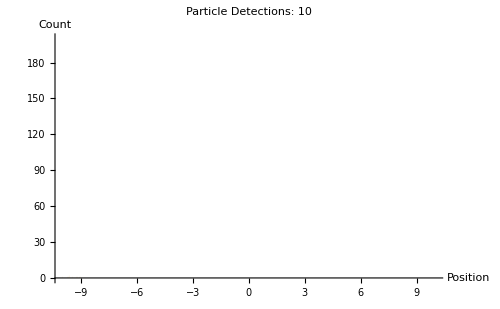
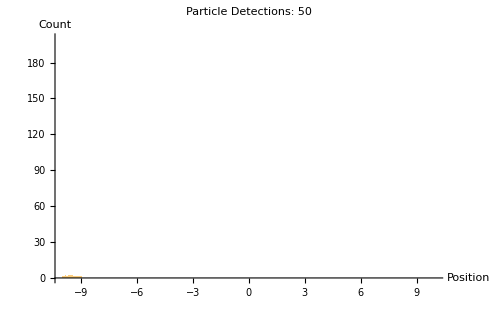
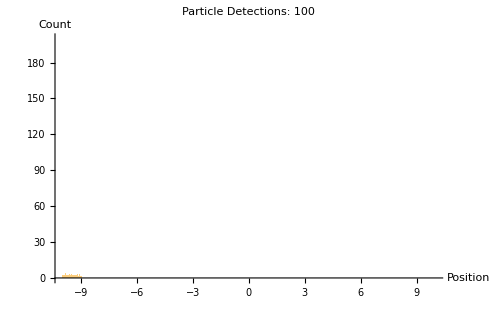
-Graphics- | -Graphics- | -Graphics-
{-Graphics-,-Graphics-,-Graphics-}⟦4⟧ | {-Graphics-,-Graphics-,-Graphics-}⟦5⟧ | {-Graphics-,-Graphics-,-Graphics-}⟦6⟧